# 6基盤ログの解析:推定ユーザーごとのアクセス推移（ユーザーストーリー）

生ログ用

オリジナルを”/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231120/T=4/_story/”とする。
実行結果が妥当かは上記と比較する。

Rev: ディレクトリ名の変更

メモ：grdmのvoc付与に関してはreferrerがないのでどのくらい取れるか確認する。

## 準備

```mathematica
start=AbsoluteTime[Date[]]
```

3.939904929230323×10^9

#### 変数

```mathematica
date="20240824"
```

20240824

```mathematica
case={"ci","cs","la","wk","jc","gr"}
```

{ci,cs,la,wk,jc,gr}

```mathematica
base["ci"]="T=ci"
base["cs"]="T=cs"
base["la"]="T=la"
base["wk"]="T=wk"
base["jc"]="T=jc"
base["gr"]="T=gr"
base["all"]="T=4"
```

T=ci

T=cs

T=la

T=wk

T=jc

T=gr

T=4

```mathematica
mountdir="/Volumes/home/NII/togo-log/rcoslogs/"
```

/Volumes/home/NII/togo-log/rcoslogs/

#### 解析用データ

```mathematica
fileliststr=Import[mountdir<>"log/D="<>date<>"/"<>"filenames","String"]
```

log-20240824.rcoslog0002.log

```mathematica
filelist=StringSplit[fileliststr]
```

{log-20240824.rcoslog0002.log}

元ログの大きさ （wc）

```mathematica
logwc=Import[mountdir<>"log/D="<>date<>"/logfiles.wc","String"]
```

24068170 330360867 12013827990 log-20240824.rcoslog0002.log

```mathematica
ckanfile=mountdir<>"crid/CIRDEV-1067_crid_list/ckan_product_crid_list.txt"
```

/Volumes/home/NII/togo-log/rcoslogs/crid/CIRDEV-1067_crid_list/ckan_product_crid_list.txt

```mathematica
ckanSt=Import[ckanfile,"String"];
```

```mathematica
(ckanName=StringSplit[ckanSt,"\n"])//Dimensions
```

{92643}

```mathematica
(ckanCridAC=Apply[Association,Map[#->#&,ckanName]])//Dimensions
```

{92643}

#### プログラム

vertexを指定してdirected-edgeを辿る部分グラフ抽出の関数：

```mathematica
directedConnectedGraphComponent[g_,v_]:=Module[{vAll,vOther,addEdge},
vAll=VertexList[g];
vOther=Complement[vAll,{v}];
addEdge=Map[#->v&,vOther];
Subgraph[g,ConnectedComponents[Flatten[{EdgeList[g],addEdge},1],v][[1]]]
]
```

グラフよりinがないノードを検出してそこから(g,v)に対して上記関数をアプライする関数：

```mathematica
vertexInGraph[g_Graph]:=Module[{deg,pos,vname},
deg=VertexInDegree[g];
pos=Position[deg,0]//Flatten//Union;
vname=VertexList[g][[pos]];
Map[directedConnectedGraphComponent[g,#]&,vname]
]
vertexInGraph[g_Integer]:=g
```

story-group-indexを各グラフにdistributeする関数：

```mathematica
distributeIdxGr[idxGr_]:=Module[
{date,idx,gr},
date=idxGr[[1]];
idx=idxGr[[2]];
gr=idxGr[[3]];
Map[{date,idx,#}&,gr]
]
```

stringからfqdnのみ抽出する関数：

```mathematica
fqdnFromPath[s_]:=StringJoin[StringSplit[s,"/"]⟦{1,3}⟧]
```

```mathematica
fqdnFromGraph[g_Graph]:=Union[Sort[Map[fqdnFromPath,VertexList[g]]]]
```

## リンク(4)

### データ(ci)

```mathematica
dir["ci"]=mountdir<>"log/D="<>date<>"/"<>base["ci"]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20240824/T=ci

#### データの読み込み

```mathematica
file["ci"]="self.1"
```

self.1

```mathematica
str["ci"]=Import[dir["ci"]<>"/"<>file["ci"],"String"];
```

```mathematica
(strSplt["ci"]=StringSplit[str["ci"],"\n"])//Length
```

6652753

```mathematica
(strSplt1["ci"]=Map[StringSplit[#,"\t"]&,strSplt["ci"]])//Dimensions
```

{6652753,15}

#### カラムポジションの調整

不要。

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
strSplt1C["ci"]=Map[ReplacePart[#,8->"https://cir.nii.ac.jp/"<>StringDrop[#[[8]],8]]&,strSplt1["ci"]];
```

レファラーのキーを削除する。

```mathematica
strSplt1CC["ci"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["ci"]];
```

時刻をMathematica標準にする。

ログのdateをWLの時間表現に変換する関数

```mathematica
logdateToTime["ci"][s_String]:=AbsoluteTime[DateList[StringTake[s,{8,-6}]]]
```

```mathematica
logdateToTime["ci"][strSplt1CC["ci"][[1]][[6]]]
```

3.93345×10^9

```mathematica
strSplt1CCC["ci"]=Map[ReplacePart[#,6->logdateToTime["ci"][#[[6]]]]&,strSplt1CC["ci"]];
```

remoteをアドレスのみに。

```mathematica
ip["ci"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
strSplt1CCCCpre["ci"]=Map[ReplacePart[#,3->ip["ci"][#[[3]]]]&,strSplt1CCC["ci"]];
```

```mathematica
strSplt1CCCCpre["ci"][[10]]//TableForm
```

2024-08-23T15:00:00Z
log.ci0001.aws.wa01.yobi
17.241.219.84
host":"-
user":"-
3.93345×10^9
method":"GET
https://cir.nii.ac.jp/crid/1380572092445211535
code":"200
size":"12252
-
agent":"Mozilla/5.0 (Macintosh; Intel Mac OS X 10_15_7) AppleWebKit/605.1.15 (KHTML, like Gecko) Version/17.4 Safari/605.1.15 (Applebot/0.1; +http://www.apple.com/go/applebot)
http_x_forwarded_for":"\"17.241.219.84\"
request_time":"0.033
upstream_response_time":"0.033"}

pathのCRID、refererのCRIDを追加。

```mathematica
toCRID[s_String/;StringMatchQ[s,RegularExpression["https://cir.nii.ac.jp/crid/.*"]]]:=StringTake[StringSplit[s,"/"][[5]],19]
```

```mathematica
strSplt1CCCC["ci"]=Map[Join[#,{toCRID[#[[8]]],toCRID[#[[11]]]}]&,strSplt1CCCCpre["ci"]];
```

```mathematica
strSplt1CCCC["ci"][[8]]//TableForm
```

2024-08-23T15:00:00Z
log.ci0001.aws.wa01.yobi
124.243.137.90
host":"-
user":"-
3.93345×10^9
method":"GET
https://cir.nii.ac.jp/crid/1130282271266216960
code":"200
size":"12678
-
agent":"Mozilla/5.0 (Windows NT 10.0; Win64; x64) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/104.0.0.0 Safari/537.36
http_x_forwarded_for":"\"124.243.137.90\"
request_time":"0.045
upstream_response_time":"0.045"}
1130282271266216960
toCRID[-]

```mathematica
accessTime["ci"]=Map[#[[6]]&,strSplt1CCCC["ci"]];
```

### データ(cs)

```mathematica
dir["cs"]=mountdir<>"log/D="<>date<>"/"<>base["cs"]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20240824/T=cs

#### データの読み込み

```mathematica
file["cs"]="self.1"
```

self.1

```mathematica
str["cs"]=Import[dir["cs"]<>"/"<>file["cs"],"String"];
```

```mathematica
(strSplt["cs"]=StringSplit[str["cs"],"\n"])//Length
```

4798

```mathematica
(strSplt1["cs"]=Map[StringSplit[#,"\t"]&,strSplt["cs"]])//Dimensions
```

{4798,15}

#### カラムポジションの調整

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: remote <- 5
4: <- 4
5: <- 6
6: date <- 3
7: <- 7
8: path <- 9
9: <- 8
10: <- 10
11: ref <- 12
12: agent <- 13
13: <- 11
14: <- 14

```mathematica
rp["cs"]={1,2,5,4,6,3,7,9,8,10,12,13,11,14}
```

{1,2,5,4,6,3,7,9,8,10,12,13,11,14}

```mathematica
(strSplt1R["cs"]=Map[#[[rp["cs"]]]&,strSplt1["cs"]])//Dimensions
```

{4798,14}

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
strSplt1R["cs"][[1]][[8]]
```

path":"/hub/home

```mathematica
pathhead["cs"]="https://jupyter.cs.rcos.nii.ac.jp"
```

https://jupyter.cs.rcos.nii.ac.jp

```mathematica
pathreplace["cs"][path_]:=Module[{pathhead,epath},
pathhead="https://jupyter.cs.rcos.nii.ac.jp";
epath=StringDrop[path,7];
If[StringTake[epath,1]=="/",pathhead<>epath,epath]
]
```

```mathematica
strSplt1C["cs"]=Map[ReplacePart[#,8->pathreplace["cs"][#[[8]]]]&,strSplt1R["cs"]];
```

レファラーのキーを削除する。(11カラム目でないといけない)

```mathematica
strSplt1CC["cs"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["cs"]];
```

レファラーになにも入っていない。設定されていないのではなく入ってきていないだけであることを確認済み。

時刻をMathematica標準にする。

ログのdateをWLの時間表現に変換する関数

```mathematica
logdateToTime["cs"][s_String]:=AbsoluteTime[DateList[StringTake[s,{16,-7}]]]
```

```mathematica
strSplt1CC["cs"][[1]][[6]]
```

{"time_local":"2024-08-24T00:28:07.036794357+09:00

```mathematica
strSplt1CCC["cs"]=Map[ReplacePart[#,6->logdateToTime["cs"][#[[6]]]]&,strSplt1CC["cs"]];
```

remoteをアドレスのみに。

```mathematica
ip["cs"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
strSplt1CCCC["cs"]=Map[ReplacePart[#,3->ip["cs"][#[[3]]]]&,strSplt1CCC["cs"]];
```

```mathematica
strSplt1CCCC["cs"][[10]]//TableForm
```

2024-08-23T15:28:24Z
log.cs0002.ksw.wa01.yobi
35.213.23.14
stream":"stdout
user":"-
3.93345×10^9
date_time":"23/Aug/2024:15:28:23 +0000
https://jupyter.cs.rcos.nii.ac.jp/hub/static/js/utils.js?v=20240820020745
method":"GET
code":"200
https://jupyter.cs.rcos.nii.ac.jp/hub/home
agent":"Mozilla/5.0 (X11; Linux x86_64) AppleWebKit/537.36 (KHTML, like Gecko) HeadlessChrome/88.0.4324.150 Safari/537.36
size":"4384
app_user":"0d90424cf9258d120979c02c1c5fb926400500b782bc8f8fe67f2df7b517a03f

```mathematica
accessTime["cs"]=Map[#[[6]]&,strSplt1CCCC["cs"]];
```

### データ(la)

```mathematica
dir["la"]=mountdir<>"log/D="<>date<>"/"<>base["la"]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20240824/T=la

laのログに関し23・9中頃よりsession_idが入る。(12 カラム目 -> 10 カラム目)

#### データの読み込み

```mathematica
file["la"]="self.1"
```

self.1

```mathematica
str["la","pre"]=Import[dir["la"]<>"/"<>file["la"],"String"];
```

```mathematica
(strSplt["la","pre"]=StringSplit[str["la","pre"],"\n"])//Length
```

54035

```mathematica
(strSplt1["la","pre"]=Map[StringSplit[#,"\t"]&,strSplt["la","pre"]])//Dimensions
```

{54035,12}

```mathematica
Map[#[[2]]&,strSplt1["la","pre"]]//Tally
```

{{log.la0002.aws.wa01.yobi,8640},{log.la0003.aws.wa01.yobi,8640},{log.la0001.aws.wa01.yobi,36755}}

"log.la0001.aws.wa01.yobi" の分離

```mathematica
(strSplt1["la","log.la0001.aws.wa01.yobi"]=Select[strSplt1["la","pre"],#[[2]]=="log.la0001.aws.wa01.yobi"&])//Dimensions
```

{36755,12}

"log.la0002.aws.wa01.yobi" の分離

```mathematica
(strSplt1["la","log.la0002.aws.wa01.yobi"]=Select[strSplt1["la","pre"],#[[2]]=="log.la0002.aws.wa01.yobi"&])//Dimensions
```

{8640,12}

"log.la0003.aws.wa01.yobi" の分離

```mathematica
(strSplt1["la","log.la0003.aws.wa01.yobi"]=Select[strSplt1["la","pre"],#[[2]]=="log.la0003.aws.wa01.yobi"&])//Dimensions
```

{8640,12}

#### カラムポジションの調整

"log.la0001.aws.wa01.yobi"

```mathematica
strSplt1["la","log.la0001.aws.wa01.yobi"][[1]]//TableForm
```

2024-08-23T15:00:03Z
log.la0001.aws.wa01.yobi
{"user":"-
date_time":"24/Aug/2024:00:00:03 +0900
method":"GET
path":"/
code":"200
size":"2
referer":"-
agent":"kube-probe/1.28+
http_x_forwarded_for":"-
session_id":"-"}

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: http_x_forwarded_for (remote) <- 11 
4: <- 8
5: <- 5
6: date <- 4
7: <- 7
8: path <- 6
9: <- 3
10: <- 12
11: ref <- 9
12: agent <- 10

```mathematica
rp["la","log.la0001.aws.wa01.yobi"]={1,2,11,8,5,4,7,6,3,12,9,10}
```

{1,2,11,8,5,4,7,6,3,12,9,10}

```mathematica
(strSplt1R["la","log.la0001.aws.wa01.yobi"]=Map[#[[rp["la","log.la0001.aws.wa01.yobi"]]]&,strSplt1["la","log.la0001.aws.wa01.yobi"]])//Dimensions
```

{36755,12}

"log.la0002.aws.wa01.yobi"

```mathematica
strSplt1["la","log.la0002.aws.wa01.yobi"][[1]]//TableForm
```

2024-08-23T15:00:00Z
log.la0002.aws.wa01.yobi
{"user":"-
date_time":"23/Aug/2024:15:00:00 +0000
method":"GET
path":"/health
code":"200
size":"2
referer":"-
agent":"kube-probe/1.28+
http_x_forwarded_for":"-
session_id":"-"}

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: http_x_forwarded_for (remote) <- 11 
4: <- 8
5: <- 5
6: date <- 4
7: <- 7
8: path <- 6
9: <- 3
10: <- 12
11: ref <- 9
12: agent <- 10

```mathematica
rp["la","log.la0002.aws.wa01.yobi"]={1,2,11,8,5,4,7,6,3,12,9,10}
```

{1,2,11,8,5,4,7,6,3,12,9,10}

```mathematica
(strSplt1R["la","log.la0002.aws.wa01.yobi"]=Map[#[[rp["la","log.la0002.aws.wa01.yobi"]]]&,strSplt1["la","log.la0002.aws.wa01.yobi"]])//Dimensions
```

{8640,12}

"log.la0003.aws.wa01.yobi"

```mathematica
strSplt1["la","log.la0003.aws.wa01.yobi"][[1]]//TableForm
```

2024-08-23T15:00:09Z
log.la0003.aws.wa01.yobi
{"user":"-
date_time":"23/Aug/2024:15:00:09 +0000
method":"GET
path":"/_chp_healthz
code":"200
size":"15
referer":"-
agent":"kube-probe/1.28+
http_x_forwarded_for":"-
session_id":"-"}

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: http_x_forwarded_for (remote) <- 11 
4: <- 8
5: <- 5
6: date <- 4
7: <- 7
8: path <- 6
9: <- 3
10: <- 12
11: ref <- 9
12: agent <- 10

```mathematica
rp["la","log.la0003.aws.wa01.yobi"]={1,2,11,8,5,4,7,6,3,12,9,10}
```

{1,2,11,8,5,4,7,6,3,12,9,10}

```mathematica
(strSplt1R["la","log.la0003.aws.wa01.yobi"]=Map[#[[rp["la","log.la0003.aws.wa01.yobi"]]]&,strSplt1["la","log.la0003.aws.wa01.yobi"]])//Dimensions
```

{8640,12}

3サービスをマージ

```mathematica
(strSplt1R["la"]=Join[strSplt1R["la","log.la0001.aws.wa01.yobi"],strSplt1R["la","log.la0002.aws.wa01.yobi"],strSplt1R["la","log.la0003.aws.wa01.yobi"]])//Dimensions
```

{54035,12}

```mathematica
strSplt1R["la"][[1]]
```

{2024-08-23T15:00:03Z,log.la0001.aws.wa01.yobi,http_x_forwarded_for":"-,size":"2,method":"GET,date_time":"24/Aug/2024:00:00:03 +0900,code":"200,path":"/,{"user":"-,session_id":"-"},referer":"-,agent":"kube-probe/1.28+}

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
pathhead["la"]="https://lms.nii.ac.jp"
```

https://lms.nii.ac.jp

```mathematica
pathreplace["la"][path_]:=Module[{pathhead,epath},
pathhead="https://lms.nii.ac.jp";
epath=StringDrop[path,7];
If[StringTake[epath,1]=="/",pathhead<>epath,epath]
]
```

```mathematica
strSplt1C["la"]=Map[ReplacePart[#,8->pathreplace["la"][#[[8]]]]&,strSplt1R["la"]];
```

レファラーのキーを削除する。(11カラム目でないといけない)

```mathematica
strSplt1CC["la"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["la"]];
```

時刻をMathematica標準にする。

```mathematica
(*logdateToTime["la"][s_String]:=AbsoluteTime[DateList[StringTake[s,{13,-6}]]]+(9*60*60)*)
```

```mathematica
logdateToTime["la"][s_String]:=AbsoluteTime[DateList[StringTake[s,{13,-6}]]]
```

```mathematica
StringTake[strSplt1CC["la"][[1]][[6]],{13,-6}]//DateList//AbsoluteTime
```

3.93345×10^9

```mathematica
strSplt1CCC["la"]=Map[ReplacePart[#,6->logdateToTime["la"][#[[6]]]]&,strSplt1CC["la"]];
```

```mathematica
strSplt1CCC["la"][[1]]//TableForm
```

2024-08-23T15:00:03Z
log.la0001.aws.wa01.yobi
http_x_forwarded_for":"-
size":"2
method":"GET
3.93345×10^9
code":"200
https://lms.nii.ac.jp/
{"user":"-
session_id":"-"}
-
agent":"kube-probe/1.28+

http_x_forwarded_for (remote)をアドレスのみに。

```mathematica
ip["la"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
(strSplt1CCCC["la"]=Map[ReplacePart[#,3->ip["la"][#[[3]]]]&,strSplt1CCC["la"]])//Dimensions
```

{54035,12}

```mathematica
strSplt1CCCC["la"][[1]]//TableForm
```

2024-08-23T15:00:03Z
log.la0001.aws.wa01.yobi
-
size":"2
method":"GET
3.93345×10^9
code":"200
https://lms.nii.ac.jp/
{"user":"-
session_id":"-"}
-
agent":"kube-probe/1.28+

```mathematica
accessTime["la"]=Map[#[[6]]&,strSplt1CCCC["la"]];
```

### データ(wk)

2024 年度に入ってから、 log.wk1001.xxx 以外に log.wk3001.xxx が挿入されているので場合わけする。

```mathematica
dir["wk"]=mountdir<>"log/D="<>date<>"/"<>base["wk"]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20240824/T=wk

#### データの読み込み

```mathematica
file["wk"]="self.1"
```

self.1

```mathematica
str["wk"]=Import[dir["wk"]<>"/"<>file["wk"],"String"];
```

```mathematica
(strSplt["wk"]=StringSplit[str["wk"],"\n"])//Length
```

4491

```mathematica
(strSplt1["wk"]=Map[StringSplit[#,"\t"]&,strSplt["wk"]])//Dimensions
```

{4491,12}

#### カラムポジションの調整

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: remote <- 3
4: <- 4
5: <- 6
6: date <- 5
7: <- 8
8: path <- 7
9: <- 9
10: <- 12
11: ref <- 10
12: agent <- 11

```mathematica
rp["wk"]={1,2,3,4,6,5,8,7,9,12,10,11}
```

{1,2,3,4,6,5,8,7,9,12,10,11}

```mathematica
(strSplt1R["wk"]=Map[#[[rp["wk"]]]&,strSplt1["wk"]])//Dimensions
```

{4491,12}

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
pathhead["wk"]="https://jdcat.jsps.go.jp"
```

https://jdcat.jsps.go.jp

```mathematica
pathreplace["wk"][path_]:=Module[{pathhead,epath},
pathhead="https://jdcat.jsps.go.jp";
epath=StringDrop[path,7];
If[StringTake[epath,1]=="/",pathhead<>epath,epath]
]
```

```mathematica
strSplt1C["wk"]=Map[ReplacePart[#,8->pathreplace["wk"][#[[8]]]]&,strSplt1R["wk"]];
```

レファラーのキーを削除する。(11カラム目でないといけない)

```mathematica
strSplt1CC["wk"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["wk"]];
```

レファラーになにも入っていない。設定されていないのではなく入ってきていないだけであることを確認済み。

時刻をMathematica標準にする。

ログのdateをWLの時間表現に変換する関数

```mathematica
logdateToTime["wk"][s_String]:=AbsoluteTime[DateList[StringTake[s,{13,-6}]]]+(9*60*60)
```

```mathematica
strSplt1CC["wk"][[1]][[6]]
```

date_time":"2024-08-23T15:00:38+0000

```mathematica
strSplt1CC["wk"][[1]][[6]]//logdateToTime["wk"]
```

3.93345×10^9

```mathematica
strSplt1CCC["wk"]=Map[ReplacePart[#,6->logdateToTime["wk"][#[[6]]]]&,strSplt1CC["wk"]];
```

remoteをアドレスのみに。

```mathematica
ip["wk"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
strSplt1CCCC["wk"]=Map[ReplacePart[#,3->ip["wk"][#[[3]]]]&,strSplt1CCC["wk"]];
```

```mathematica
strSplt1CCCC["wk"][[26]]//TableForm
```

2024-08-23T15:08:15Z
log.wk1001.oci.wa01.yobi
173.252.107.116
user":"-
method":"GET
3.93345×10^9
code":"200
https://jdcat.jsps.go.jp/records/32442/export/bibtex
size":"31
http_x_forwarded_for":"173.252.107.116"}
-
agent":"facebookexternalhit/1.1 (+http://www.facebook.com/externalhit_uatext.php)

```mathematica
accessTime["wk"]=Map[#[[6]]&,strSplt1CCCC["wk"]];
```

### データ(jc) 作り中

2024 年度に入ってから、 log.wk1001.xxx 以外に log.wk3001.xxx が挿入されているので場合わけする。

```mathematica
dir["wk"]=mountdir<>"log/D="<>date<>"/"<>base["jc"]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20240824/T=wk

#### データの読み込み

```mathematica
file["wk"]="self.1"
```

self.1

```mathematica
str["wk"]=Import[dir["wk"]<>"/"<>file["wk"],"String"];
```

```mathematica
(strSplt["wk"]=StringSplit[str["wk"],"\n"])//Length
```

4491

```mathematica
(strSplt1["wk"]=Map[StringSplit[#,"\t"]&,strSplt["wk"]])//Dimensions
```

{4491,12}

#### カラムポジションの調整

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: remote <- 3
4: <- 4
5: <- 6
6: date <- 5
7: <- 8
8: path <- 7
9: <- 9
10: <- 12
11: ref <- 10
12: agent <- 11

```mathematica
rp["wk"]={1,2,3,4,6,5,8,7,9,12,10,11}
```

{1,2,3,4,6,5,8,7,9,12,10,11}

```mathematica
(strSplt1R["wk"]=Map[#[[rp["wk"]]]&,strSplt1["wk"]])//Dimensions
```

{4491,12}

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
pathhead["wk"]="https://jdcat.jsps.go.jp"
```

https://jdcat.jsps.go.jp

```mathematica
pathreplace["wk"][path_]:=Module[{pathhead,epath},
pathhead="https://jdcat.jsps.go.jp";
epath=StringDrop[path,7];
If[StringTake[epath,1]=="/",pathhead<>epath,epath]
]
```

```mathematica
strSplt1C["wk"]=Map[ReplacePart[#,8->pathreplace["wk"][#[[8]]]]&,strSplt1R["wk"]];
```

レファラーのキーを削除する。(11カラム目でないといけない)

```mathematica
strSplt1CC["wk"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["wk"]];
```

レファラーになにも入っていない。設定されていないのではなく入ってきていないだけであることを確認済み。

時刻をMathematica標準にする。

ログのdateをWLの時間表現に変換する関数

```mathematica
logdateToTime["wk"][s_String]:=AbsoluteTime[DateList[StringTake[s,{13,-6}]]]+(9*60*60)
```

```mathematica
strSplt1CC["wk"][[1]][[6]]
```

date_time":"2024-08-23T15:00:38+0000

```mathematica
strSplt1CC["wk"][[1]][[6]]//logdateToTime["wk"]
```

3.93345×10^9

```mathematica
strSplt1CCC["wk"]=Map[ReplacePart[#,6->logdateToTime["wk"][#[[6]]]]&,strSplt1CC["wk"]];
```

remoteをアドレスのみに。

```mathematica
ip["wk"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
strSplt1CCCC["wk"]=Map[ReplacePart[#,3->ip["wk"][#[[3]]]]&,strSplt1CCC["wk"]];
```

```mathematica
strSplt1CCCC["wk"][[26]]//TableForm
```

2024-08-23T15:08:15Z
log.wk1001.oci.wa01.yobi
173.252.107.116
user":"-
method":"GET
3.93345×10^9
code":"200
https://jdcat.jsps.go.jp/records/32442/export/bibtex
size":"31
http_x_forwarded_for":"173.252.107.116"}
-
agent":"facebookexternalhit/1.1 (+http://www.facebook.com/externalhit_uatext.php)

```mathematica
accessTime["wk"]=Map[#[[6]]&,strSplt1CCCC["wk"]];
```

### データ(gr)

```mathematica
dir["gr"]=mountdir<>"log/D="<>date<>"/"<>base["gr"]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20240824/T=gr

#### データの読み込み

```mathematica
file["gr"]="self.1"
```

self.1

```mathematica
str["gr"]=Import[dir["gr"]<>"/"<>file["gr"],"String"];
```

```mathematica
(strSplt["gr"]=StringSplit[str["gr"],"\n"])//Length
```

844896

```mathematica
(strSplt1["gr","pre"]=Map[StringSplit[#,"\t"]&,strSplt["gr"]])//Dimensions
```

{844896,21}

```mathematica
(strSplt1["gr"]=Cases[strSplt1["gr","pre"],x_/;Length[x]==21])//Dimensions
```

{844896,21}

#### カラムポジションの調整

CiRとカラムポジションをあわせる。
1: <- 1
2: <- 2
3: remote <- 10
4: host <- 7
5: user <- 15
6: date <- 13
7: method <- 3
8: path <- 4
9: code <- 6
10: size <- 12
11: ref <- 9
12: agent <- 5

```mathematica
rp["gr"]={1,2,10,7,15,13,3,4,6,12,9,5}
```

{1,2,10,7,15,13,3,4,6,12,9,5}

```mathematica
(strSplt1R["gr"]=Map[#[[rp["gr"]]]&,strSplt1["gr"]])//Dimensions
```

{844896,12}

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
pathhead["gr"]="https://rdm.nii.go.jp"
```

https://rdm.nii.go.jp

```mathematica
pathreplace["gr"][path_]:=Module[{pathhead,epath},
pathhead="https://rdm.nii.go.jp";
epath=StringDrop[path,7];
epath=StringSplit[epath," "][[1]];
If[StringTake[epath,1]=="/",pathhead<>epath,epath]
]
```

```mathematica
strSplt1C["gr"]=Map[ReplacePart[#,8->pathreplace["gr"][#[[8]]]]&,strSplt1R["gr"]];
```

Part::partw: Part 1 of {} does not exist.

StringTake::strse: String or list of strings expected at position 1 in StringTake[{}⟦1⟧,1].

Part::partw: Part 1 of {} does not exist.

StringTake::strse: String or list of strings expected at position 1 in StringTake[{}⟦1⟧,1].

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringTake::strse: String or list of strings expected at position 1 in StringTake[{}⟦1⟧,1].

General::stop: Further output of StringTake::strse will be suppressed during this calculation.

レファラーのキーを削除する。(11カラム目でないといけない)

```mathematica
strSplt1CC["gr"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["gr"]];
```

レファラーになにも入っていない。設定されていないのではなく入ってきていないだけであることを確認済み。

時刻をMathematica標準にする。

ログのdateをWLの時間表現に変換する関数（日本時間）

```mathematica
logdateToTime["gr"][s_String]:=AbsoluteTime[DateList[StringTake[s,{13,-1}]]]+(9*60*60)
```

```mathematica
strSplt1CC["gr"][[1]][[6]]
```

date_time":"2024-08-23T14:59:02.475964243+00:00

```mathematica
strSplt1CC["gr"][[1]][[6]]//logdateToTime["gr"]
```

3.93348×10^9

```mathematica
strSplt1CCC["gr"]=Map[ReplacePart[#,6->logdateToTime["gr"][#[[6]]]]&,strSplt1CC["gr"]];
```

```mathematica
strSplt1CCC["gr"]//Length
```

844896

```mathematica
Cases[strSplt1CCC["gr"],x_/;x[[6]]<=0]
```

{}

remoteをアドレスのみに。

```mathematica
ip["gr"][str_]:=Module[{s},
s=StringSplit[str,"\":\""];
If[Length[s]==1,"",s[[2]]]
]
```

```mathematica
strSplt1CCCC["gr"]=Map[ReplacePart[#,3->ip["gr"][#[[3]]]]&,strSplt1CCC["gr"]];
```

```mathematica
strSplt1CCCC["gr"][[26]]//TableForm
```

2024-08-23T15:09:02Z
log.gr0001.aws.wa01.yobi

host":"ip-10-20-1-17.ap-northeast-1.compute.internal
user":"
3.93348×10^9
{"method":"GET
https://rdm.nii.go.jp/v2/nodes/gvswq/files/
code":"
size":"-

agent":"

```mathematica
accessTime["gr"]=Map[#[[6]]&,strSplt1CCCC["gr"]];
```

### データの合成

ソートも行う。

ソートキーを策定：

3項のソースアドレス

12項のユーザーエージェント

6項のアクセス時刻

```mathematica
(*Timing[(strSplt1CCCC[4]=SortBy[Join[strSplt1CCCC["ci"],strSplt1CCCC["cs"],strSplt1CCCC["la"],strSplt1CCCC["wk"]],{#[[3]],#[[12]],#[[6]]}&])//Dimensions]*)
```

```mathematica
Timing[(strSplt1CCCC[4]=SortBy[Join[strSplt1CCCC["ci"],strSplt1CCCC["cs"],strSplt1CCCC["la"],strSplt1CCCC["wk"],strSplt1CCCC["gr"]],{#[[3]],#[[12]],#[[6]]}&])//Dimensions]
```

{107.105,{7560973}}

抽出ログの行インデックスをアペンド:

```mathematica
apIdx[4]=Table[i,{i,Length[strSplt1CCCC[4]]}];
```

```mathematica
(idxLog[4]=Map[Append[#[[1]],#[[2]]]&,Transpose[{strSplt1CCCC[4],apIdx[4]}]])//Dimensions
```

{7560973}

```mathematica
accessTime[4]=Map[#[[6]]&,idxLog[4]];
```

```mathematica
Cases[accessTime[4],x_/;x<0]//Length
```

0

```mathematica
(unexTimePos=Position[accessTime[4],x_/;x<0]//Flatten)//Length
```

0

怪しいタイムスタンプが多すぎる。-> 新しく入ったjcが原因、あとで処理を追加する。
T=wk/exec にて対応済み。

```mathematica
accessTime[4]//Min
```

3.93341×10^9

### ckanデータの処理(基盤全て)

CKAN-CRIDの存在確認とハッシュの生成：

パスのハッシュ：

```mathematica
(ckanPathE[4]=Map[ckanCridAC[#[[-3]]]&,idxLog[4]])//Dimensions
```

{7560973}

```mathematica
(ckanCridPLogPos[4]=Flatten[Position[ckanPathE[4],_String,{1}]])//Length
```

5643

```mathematica
(ckanCridPLogPosAC[4]=Association[Map[#->#&,ckanCridPLogPos[4]]])//Length
```

5643

リファラーのハッシュ：

```mathematica
(ckanRefE[4]=Map[ckanCridAC[#[[-2]]]&,idxLog[4]])//Dimensions
```

{7560973}

```mathematica
(ckanCridRLogPos[4]=Flatten[Position[ckanRefE[4],_String,{1}]])//Length
```

1

```mathematica
(ckanCridRLogPosAC[4]=Association[Map[#->#&,ckanCridRLogPos[4]]])//Length
```

1

パス or リファラーのハッシュ：

```mathematica
(ckanCridPRLogPos[4]=Union[ckanCridPLogPos[4],ckanCridRLogPos[4]])//Length
```

5644

```mathematica
(ckanCridPRLogPosAC[4]=Association[Map[#->#&,ckanCridPRLogPos[4]]])//Length
```

5644

## リンク(ci)

```mathematica
Timing[(strSplt1CCCC["ci"]=SortBy[strSplt1CCCC["ci"],{#[[3]],#[[12]],#[[6]]}&])//Dimensions]
```

{99.2498,{6652753,17}}

抽出ログの行インデックスをアペンド

```mathematica
apIdx["ci"]=Table[i,{i,Length[strSplt1CCCC["ci"]]}];
```

```mathematica
idxLog["ci"]=Map[Append[#[[1]],#[[2]]]&,Transpose[{strSplt1CCCC["ci"],apIdx["ci"]}]];
```

```mathematica
idxLog["ci"][[1]]//TableForm
```

2024-08-24T14:09:22Z
log.ci0001.aws.wa01.yobi
100.10.11.171
host":"-
user":"-
3.93353×10^9
method":"GET
https://cir.nii.ac.jp/crid/1524232505008572416/mendeley
code":"200
size":"453
-
agent":"Mozilla/5.0 (Linux; Android 8.0; Pixel 2 Build/OPD3.170816.012) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/40.0.4579.1105 Mobile Safari/537.36
http_x_forwarded_for":"\"100.10.11.171\"
request_time":"0.020
upstream_response_time":"0.021"}
1524232505008572416
toCRID[-]
1

### ckanデータの処理(ciのみ)

CKAN-CRIDの存在確認：

```mathematica
(ckanPathE["ci"]=Map[ckanCridAC[#[[-3]]]&,idxLog["ci"]])//Dimensions
```

{6652753}

```mathematica
ckanCridPlist=Cases[ckanPathE["ci"],_String];
```

```mathematica
ckanRefE=.
```

```mathematica
ckanRefE["ci"]=Map[ckanCridAC[#[[-2]]]&,idxLog["ci"]];
```

```mathematica
ckanCridRlist=Cases[ckanRefE["ci"],_String]
```

{1690857923900730752}

```mathematica
ckanCridPRU=Union[ckanCridPlist,ckanCridRlist];
```

```mathematica
ckanCridPRACQ=Association[Map[#->True&,ckanCridPRU]];
```

## ユーザー生成(4)

各条件のキーを策定：

3項のソースアドレス

12項のユーザーエージェント

6項のアクセス時刻

まず推定ユーザーごとにgathgerする。

#### ユーザー生成

ソースアドレスとユーザーエージェントをキーにしてsplitする。

```mathematica
(idxLogS[4]=Split[idxLog[4],#1[[3]]==#2[[3]]&&#1[[12]]==#2[[12]]&])//Length
```

710485

上記の数が推定ユーザー数。

## グラフ生成(4):inf

#### Op 1

ストーリー分割：

時間設定をinfにすることによりアクセス時間では分割しない。
1. ユーザーごとに分割 -> userGr,userGrIdx
2. 繋がらないエッジで分割 -> user2GrIdx
3. 上記の各グラフより in がないVertexを起点としてoutで辿れるパスにより各サブグラフを抽出 -> storyGrIdx
　のちに扱いやすい構造にする。

0. 時間で分割しない -> 全てを要素1のリストにする：

```mathematica
Timing[(idxLogSinf[4]=Map[Split[#,#2[[6]]-#1[[6]]<=Infinity&]&,idxLogS[4]])//Dimensions]
```

{15.1955,{710485,1}}

ユーザーストーリーグループに対応するログを参照する関数：

```mathematica
refstglog[4][g_]:={g[[1]],g[[3]],Part[idxLogSinf[4],g[[2,1]],g[[2,2]]]}
```

#### Op 2

<<< Saveデータを読んだ時はここから飛ばす。 >>>

1. ユーザーごとのグラフ生成：

エッジルール作成（この時点でエッジ以外の情報が落ちる、アクセス時刻とログ行インデックスをエッジに設定する）：

```mathematica
userGrER[4]=Map[Map[DirectedEdge[#[[11]],#[[8]],{#[[6]],#[[-1]]}]&,#]&,idxLogSinf[4],{2}];
```

```mathematica
userGrER[4][[2]]
```

{{https://rdm.nii.go.jp/robots.txt{3.93353×10^9,799478}}}

```mathematica
(userGr[4]=Map[Graph[#,VertexLabels->Automatic]&,userGrER[4],{2}])//Length
```

710485

上記がユーザー数。

ここでindexを作成。{date,{userID, log-groupID}, G} とする。

```mathematica
userGrIdx[4]=MapIndexed[{date,#2,#1}&,userGr[4],{2}]; (**)
```

2. ユーザーごとのグラフをさらにエッジでつながらない部分グラフに分ける：

```mathematica
Timing[(user2GrIdx[4]=Map[{#[[1]],#[[2]],WeaklyConnectedGraphComponents[#[[3]]]}&,userGrIdx[4],{2}])//Dimensions] (**)
```

{615.765,{710485,1,3}}

3. 分けられた各グラフをさらにinがないノードをスタートとするグラフに分ける：

```mathematica
AbsoluteTiming[(storyGrIdx[4]=ParallelMap[vertexInGraph,user2GrIdx[4],{4}])//Dimensions ](**)
```

Part::partw: Part 1 of {} does not exist.

StringTake::strse: String or list of strings expected at position 1 in StringTake[{}⟦1⟧,1].

Part::partw: Part 1 of {} does not exist.

StringTake::strse: String or list of strings expected at position 1 in StringTake[{}⟦1⟧,1].

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringTake::strse: String or list of strings expected at position 1 in StringTake[{}⟦1⟧,1].

General::stop: Further output of StringTake::strse will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringTake::strse: String or list of strings expected at position 1 in StringTake[{}⟦1⟧,1].

Part::partw: Part 1 of {} does not exist.

StringTake::strse: String or list of strings expected at position 1 in StringTake[{}⟦1⟧,1].

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringTake::strse: String or list of strings expected at position 1 in StringTake[{}⟦1⟧,1].

General::stop: Further output of StringTake::strse will be suppressed during this calculation.

{163.218,{710485,1,3}}

扱いやすい構造にする。-> storyGrIdxFlDs[4]

グラフリストをflatten:

```mathematica
(storyGrIdxFl[4]=Map[{#[[1]],#[[2]],Flatten[#[[3]]]}&,Flatten[storyGrIdx[4],1]])//Dimensions
```

{710485,3}

各グラフに{userID, story-groupID}をdistribute:

```mathematica
(storyGrIdxFlDs[4]=Flatten[Map[distributeIdxGr,storyGrIdxFl[4]],1])//Dimensions
```

{728416,3}

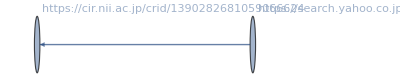
{20240824,{201,1},-Graphics-}

```mathematica
storyGrIdxFlDs[4][[200]]
```

4. 不要と思われるvertexを削除(1)：

```mathematica
(storyGrIdxFlDsVD1[4]=Map[{#[[1]],#[[2]],If[VertexQ[#[[3]],"-"],VertexDelete[#[[3]],"-"],#[[3]]]}&,storyGrIdxFlDs[4]])//Dimensions
```

{728416,3}

5. 不要と思われるvertexを削除(2)：

rm候補のパターン：

```mathematica
rmpattAll[4]={rmpatt[4][1]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/hub/static.*"],
rmpatt[4][2]=RegularExpression["https://jdcat.jsps.go.jp/api.*"],
rmpatt[4][3]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/hub/.*api.*"],
rmpatt[4][4]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/user/.*/api.*"],
rmpatt[4][5]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/img.*"],
rmpatt[4][6]=RegularExpression["https://.*/.*\\.svg"],
rmpatt[4][7]=RegularExpression["https://.*/.*\\.js"],
rmpatt[4][8]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/.*\\.js\\?.*"],
rmpatt[4][9]=RegularExpression["https://jdcat.jsps.go.jp/.*\\.js\\?.*"],
rmpatt[4][10]=RegularExpression["https://.*/.*\\.woff2.*"],
rmpatt[4][11]=RegularExpression["https://.*/.*\\.css"],
rmpatt[4][12]=RegularExpression["https://.*/css/.*"],
rmpatt[4][13]=RegularExpression["https://.*/.*\\.favicon.ico"],
rmpatt[4][14]="https://jdcat.jsps.go.jp/get_search_setting",
rmpatt[4][15]="https://jdcat.jsps.go.jp/facet-search/get-title-and-order"
}
```

{RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/hub/static.*],RegularExpression[https://jdcat.jsps.go.jp/api.*],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/hub/.*api.*],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/user/.*/api.*],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/img.*],RegularExpression[https://.*/.*\.svg],RegularExpression[https://.*/.*\.js],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/.*\.js\?.*],RegularExpression[https://jdcat.jsps.go.jp/.*\.js\?.*],RegularExpression[https://.*/.*\.woff2.*],RegularExpression[https://.*/.*\.css],RegularExpression[https://.*/css/.*],RegularExpression[https://.*/.*\.favicon.ico],https://jdcat.jsps.go.jp/get_search_setting,https://jdcat.jsps.go.jp/facet-search/get-title-and-order}

rm候補のパターンから削除頂点リストを生成（参考）：

```mathematica
createRmList[gr_,rmpatt_]:=Module[{vlist},
vlist=VertexList[gr];
Union[Flatten[Table[Cases[vlist,x_/;StringMatchQ[x,rmpatt[[n]]]],{n,Length[rmpatt]}]]]
]
```

rm候補のパターンを指定してグラフからマッチする頂点を削除する関数：

```mathematica
rmV[gr_,rmpatt_]:=Module[{vlist,pathlist},
vlist=VertexList[gr];
pathlist=Union[Flatten[Table[Cases[vlist,x_/;StringMatchQ[x,rmpatt[[n]]]],{n,Length[rmpatt]}]]];
VertexDelete[gr,pathlist]
]
```

```mathematica
(storyGrIdxFlDsVD2[4]=Map[{#[[1]],#[[2]],rmV[#[[3]],rmpattAll[4]]}&,storyGrIdxFlDsVD1[4]])//Dimensions
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[If[StringTake[{}⟦1⟧,1]==/,pathhead$151962<>epath$151962,epath$151962],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/hub/static.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[If[StringTake[{}⟦1⟧,1]==/,pathhead$384448<>epath$384448,epath$384448],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/hub/static.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[If[StringTake[{}⟦1⟧,1]==/,pathhead$523440<>epath$523440,epath$523440],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/hub/static.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{728416,3}

6. 以上の操作により不正となったグラフを削除(対象をpick)：

ノード数 >= 2：

```mathematica
pickPos[4][1]=Flatten[Position[Map[VertexCount[#[[3]]]&,storyGrIdxFlDsVD2[4]],x_/;x>=2]];
```

```mathematica
(storyGrIdxFlDs2[4]=storyGrIdxFlDsVD2[4][[pickPos[4][1]]])//Dimensions
```

{116020,3}

エッジ数 >= 1：

```mathematica
pickPos[4][2]=Flatten[Position[Map[EdgeCount[#[[3]]]&,storyGrIdxFlDs2[4]],x_/;x>=1]];
```

```mathematica
(storyGrIdxFlDs3[4]=storyGrIdxFlDs2[4][[pickPos[4][2]]])//Dimensions
```

{99185,3}

上が分離されたストーリー

```mathematica
storyGrIdxFlDs3[4][[1]]
```

{20240824,{1,1},}

#### Op 2.1 : save

```mathematica
savedir=mountdir<>"log/D="<>date<>"/T=4/_story"
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20240824/T=4/_story

```mathematica
SetDirectory[savedir]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20240824/T=4/_story

```mathematica
Directory[]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20240824/T=4/_story

```mathematica
Timing[Save["storyGrIdxFlDs3.save",storyGrIdxFlDs3]]
Timing[Save["storyGrIdxFlDs3.save",toCRID]]
Timing[Save["ckan.save",ckanName]]
Timing[Save["ckan.save",ckanCridAC]]
Timing[Save["ckan.save",ckanCridPLogPosAC]]
Timing[Save["ckan.save",ckanCridRLogPosAC]]
Timing[Save["ckan.save",ckanCridPRLogPosAC]]
Timing[Save["ckan.save",ckanCridPRACQ]]
```

{42.8263,Null}

{0.000342,Null}

{0.20277,Null}

{0.556938,Null}

{0.010478,Null}

{0.000269,Null}

{0.010019,Null}

{0.011715,Null}

<<< Saveデータを読んだ時はここまで飛ばす。 >>>

#### Op 3

Saveデータがある時は読み込む：

```mathematica
(*SetDirectory["/Volumes/elecom/NII/togo-log/rcoslogs/log/D="<>date<>"/"<>base["all"]<>"/_story"]*)
```

SetDirectory::cdir: Cannot set current directory to /Volumes/elecom/NII/togo-log/rcoslogs/log/D=20240824/T=4/_story.

$Failed

```mathematica
(*Timing[Get["storyGrIdxFlDs.save"];]*)
```

Get::noopen: Cannot open storyGrIdxFlDs.save.

{0.011721,Null}

## Analysis

### Analysis 1 graph property

基本属性

エッジ:

```mathematica
(eltbl[4]=Table[EdgeList[storyGrIdxFlDs3[4][[i]][[3]]],{i,Length[storyGrIdxFlDs3[4]]}])//Dimensions
```

{99185}

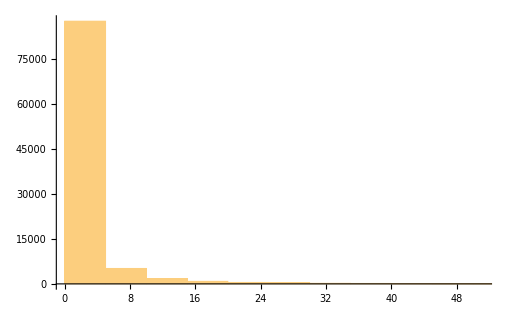

```mathematica
Histogram[Map[Length,eltbl[4]],{5}]
```

ノード:

```mathematica
(vltbl[4]=Table[VertexList[storyGrIdxFlDs3[4][[i]][[3]]],{i,Length[storyGrIdxFlDs3[4]]}])//Dimensions
```

{99185}

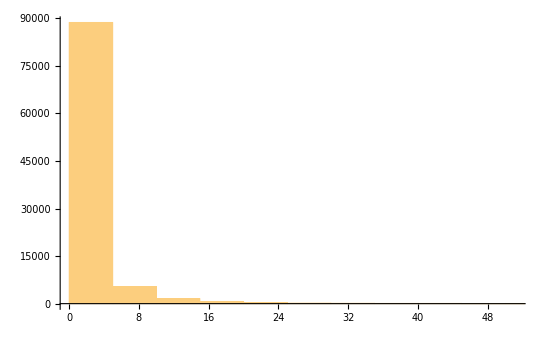

```mathematica
Histogram[Map[Length,vltbl[4]],{5}]
```

アクセス時刻:

```mathematica
(acct[4]=Map[#[[3,1]]&,eltbl[4],{2}])//Dimensions
```

{99185}

滞留時間：

```mathematica
(accspanMin[4]=Map[Max[#]-Min[#]&,acct[4]]/60)//Dimensions
```

{99185}

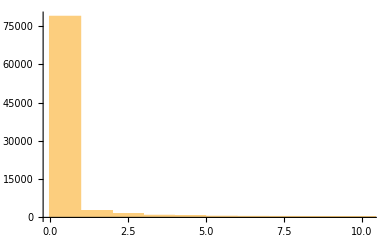

```mathematica
Histogram[accspanMin[4],{1}]
```

スタートノードが最小時刻になっていない。調整が必要か？

E/V ratio:

```mathematica
(ratioEV[4]=Map[Length,eltbl[4]]/Map[Length,vltbl[4]]//N)//Dimensions
```

{99185}

TV ratio :

```mathematica
(ratioTV[4]=acct[4]/Map[Length,vltbl[4]])//Dimensions
```

{99185}

TE ratio:

```mathematica
(ratioTE[4]=acct[4]/Map[Length,eltbl[4]])//Dimensions
```

{99185}

### Analysis 2 base interaction

リクエストパスから基盤名だけをとりだし、基盤連携を見る。

```mathematica
(GrBases[4]=Map[fqdnFromGraph[#[[3]]]&,storyGrIdxFlDs3[4]])//Dimensions
```

Part::partw: Part {1,3} of {} does not exist.

StringJoin::string: String expected at position 1 in StringJoin[{}⟦{1,3}⟧].

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[If[StringTake[{}⟦1⟧,1]==/,pathhead$151372<>epath$151372,epath$151372],/].

Part::partw: Part {1,3} of StringSplit[If[StringTake[{}⟦1⟧,1]==/,pathhead$151372<>epath$151372,epath$151372],/] does not exist.

StringJoin::string: String expected at position 1 in StringJoin[StringSplit[If[StringTake[{}⟦1⟧,1]==/,pathhead$151372<>epath$151372,epath$151372],/]⟦{1,3}⟧].

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[If[StringTake[{}⟦1⟧,1]==/,pathhead$383858<>epath$383858,epath$383858],/].

Part::partw: Part {1,3} of StringSplit[If[StringTake[{}⟦1⟧,1]==/,pathhead$383858<>epath$383858,epath$383858],/] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in StringJoin[StringSplit[If[StringTake[{}⟦1⟧,1]==/,pathhead$383858<>epath$383858,epath$383858],/]⟦{1,3}⟧].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[If[StringTake[{}⟦1⟧,1]==/,pathhead$522850<>epath$522850,epath$522850],/].

General::stop: Further output of StringSplit::strse will be suppressed during this calculation.

{99185}

NII基盤(4基盤以外も)へのアクセスを見る。

```mathematica
niidnpos=Flatten[Position[Map[StringMatchQ[#,RegularExpression[".*nii.ac.jp.*"]]||StringMatchQ[#,RegularExpression[".*jdcat.jsps.go.jp.*"]]&,Flatten[GrBases[4]]//Union],True]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*nii.ac.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*jdcat.jsps.go.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{13.230.241.81}⟦{1,3}⟧],RegularExpression[.*nii.ac.jp.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{28,29,37,38,49,94,132,133,134,135,141,143,161,195,196,246,267,268,279,285,365,384,444,452,524,701,719,747,758,935,987,1009}

```mathematica
(Flatten[GrBases[4]]//Union)[[niidnpos]]
```

{http:ci.nii.ac.jp,http:cir.nii.ac.jp,http:jdcat.jsps.go.jp,http:jdcat.jsps.go.jp:80,http:lms.nii.ac.jp,https:auth.cir.nii.ac.jp,https:ci.nii.ac.jp,https:ci.nii.ac.jp:443,https:ci-nii-ac-jp.cdn.ampproject.org,https:cir.nii.ac.jp,https:contents.nii.ac.jp,https:core.orthros.gakunin.nii.ac.jp,https:dsc.repo.nii.ac.jp,https:ge.nii.ac.jp,https:ge.nii.ac.jp:443,https:idp.nii.ac.jp,https:jdcat.jsps.go.jp,https:jdcat.jsps.go.jp:443,https:jupyter.cs.rcos.nii.ac.jp,https:kaken.nii.ac.jp,https:library.unii.ac.jp,https:lms.nii.ac.jp,https:nrid.nii.ac.jp,https:office.gakunin.nii.ac.jp,https:rcos.nii.ac.jp,https:support.nii.ac.jp,https:tohtech.repo.nii.ac.jp,https:webfront.nii.ac.jp:443,https:wiki.nii.ac.jp,https:www.nii.ac.jp,https:www.unii.ac.jp,https:ycu.repo.nii.ac.jp}

```mathematica
(GrNiiBases[4]=Map[Cases[#,x_/;StringMatchQ[x,RegularExpression[".*nii.ac.jp.*"]]||StringMatchQ[x,RegularExpression[".*jdcat.jsps.go.jp.*"]]]&,GrBases[4]])//Dimensions
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*nii.ac.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*jdcat.jsps.go.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[StringSplit[If[StringTake[Part[«2»],1]==/,pathhead$151372<>epath$151372,epath$151372],/]⟦{1,3}⟧],RegularExpression[.*nii.ac.jp.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{99185}

```mathematica
Map[Length,GrBases[4]]//Tally
```

{{11,1},{2,91697},{5,1},{4,1},{3,16},{17,1},{13,1},{138,1},{1,7466}}

```mathematica
(GrBasesTly[4]=Tally[GrBases[4]])//Dimensions
```

{1082,2}

```mathematica
Map[Length,GrNiiBases[4]]//Tally
```

{{0,107},{1,94153},{2,4925}}

```mathematica
(GrNiiBasesTly[4]=Tally[GrNiiBases[4]])//Dimensions
```

{35,2}

```mathematica
GrNiiBasesTly[4]//TableForm
```

| 107
https:cir.nii.ac.jp | 93917
https:lms.nii.ac.jp | 179
https:ci.nii.ac.jp
https:cir.nii.ac.jp | 3782
https:cir.nii.ac.jp
https:lms.nii.ac.jp | 15
https:cir.nii.ac.jp
https:www.unii.ac.jp | 1
https:jdcat.jsps.go.jp | 53
http:ci.nii.ac.jp
https:cir.nii.ac.jp | 71
https:cir.nii.ac.jp
https:support.nii.ac.jp | 58
https:auth.cir.nii.ac.jp
https:cir.nii.ac.jp | 3
https:cir.nii.ac.jp
https:www.nii.ac.jp | 9
https:idp.nii.ac.jp
https:lms.nii.ac.jp | 10
https:lms.nii.ac.jp
https:wiki.nii.ac.jp | 3
https:cir.nii.ac.jp
https:ge.nii.ac.jp:443 | 9
https:cir.nii.ac.jp
https:nrid.nii.ac.jp | 5
https:cir.nii.ac.jp
https:kaken.nii.ac.jp | 7
https:jupyter.cs.rcos.nii.ac.jp | 4
https:core.orthros.gakunin.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 2
https:ci-nii-ac-jp.cdn.ampproject.org
https:cir.nii.ac.jp | 1
https:ci.nii.ac.jp:443
https:cir.nii.ac.jp | 878
https:cir.nii.ac.jp
https:rcos.nii.ac.jp | 2
http:lms.nii.ac.jp
https:lms.nii.ac.jp | 3
https:cir.nii.ac.jp
https:webfront.nii.ac.jp:443 | 1
https:cir.nii.ac.jp
https:dsc.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:office.gakunin.nii.ac.jp | 3
https:cir.nii.ac.jp
https:tohtech.repo.nii.ac.jp | 1
https:lms.nii.ac.jp
https:www.nii.ac.jp | 3
https:cir.nii.ac.jp
https:library.unii.ac.jp | 2
http:cir.nii.ac.jp
https:cir.nii.ac.jp | 3
https:cir.nii.ac.jp
https:ge.nii.ac.jp | 47
https:contents.nii.ac.jp
https:lms.nii.ac.jp | 1
http:jdcat.jsps.go.jp
https:jdcat.jsps.go.jp | 1
https:cir.nii.ac.jp
https:ycu.repo.nii.ac.jp | 1
http:jdcat.jsps.go.jp:80
https:jdcat.jsps.go.jp | 1
https:jdcat.jsps.go.jp
https:jdcat.jsps.go.jp:443 | 1

グラフが多すぎるので選び方を考え中。

ここから、Idpで認証されたログはIdpがリファラーとして入ってくるが、認証元情報がはいらないため基盤連携のグラフに組み込まれない。
 一方で、Idpを遮蔽して認証元からアクセス先へのエッジは発生する。

### Analysis 3 time series

```mathematica
accessFirst=(Cases[accessTime[4],x_/;x>0]//Min)
```

3.93341×10^9

```mathematica
accessLast=(Cases[accessTime[4],x_/;x>0]//Max)
```

3.93357×10^9

```mathematica
Sort[accessTime["ci"]]//Length
```

6652753

```mathematica
BC600["ci"]=BinCounts[Sort[accessTime["ci"]],{accessFirst,accessLast,60*10}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,57479,57854,50335,42381,50671,52947,61427,68255,58167,55478,52013,52104,59959,57650,48428,40789,35501,48087,58764,50473,37921,31187,28704,29154,31715,32773,44017,44918,38200,47723,41759,46481,41792,42237,36826,43323,51866,51753,45992,38550,36869,48122,53678,44304,37569,38236,40124,43946,56359,59930,49610,47481,45416,57029,63061,58149,45193,40540,36783,41302,52594,54144,42199,44279,50309,57322,59066,52904,47027,45884,43738,50320,45759,43221,42629,44166,43851,41228,42646,50415,45168,39439,37429,45462,47280,48057,39779,32477,30718,31384,32275,27027,26132,29924,28390,34904,37099,48122,45588,45080,52090,60414,61978,56766,47066,44341,43852,46970,44875,53226,49652,37996,36994,50351,56893,52277,44422,41195,35073,42010,55286,52683,43783,43417,41283,44682,51499,54369,43280,35492,31122,39078,45420,42911,47361,46909,56039,65802,62081,56931,47026,49218,56139,67712,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
BC600["cs"]=BinCounts[Sort[accessTime["cs"]],{accessFirst,accessLast,60*10}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,3,35,2,0,1,10,0,0,1,2,0,10,0,36,2,0,0,10,0,0,0,1,0,4009,0,34,2,0,0,11,0,0,1,0,0,10,0,34,3,0,0,10,0,0,0,0,0,11,0,34,2,0,0,11,0,1,0,2,0,10,0,34,3,0,0,10,0,0,1,0,2,11,0,34,2,0,0,10,0,0,1,0,0,10,0,34,2,0,0,11,0,67,1,0,0,10,1,34,2,0,0,10,0,0,0,1,0,10,0,34,2,0,0,12,0,0,0,0,0,10,1,34,4,0,0,10,0,1,3,0,0,10,21,34,2,1,0,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
BC600["la"]=BinCounts[Sort[accessTime["la"]],{accessFirst,accessLast,60*10}]
```

{120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,242,244,519,377,587,1007,283,276,271,261,258,287,324,264,240,241,242,243,243,240,241,304,336,326,307,355,319,384,406,324,323,352,312,452,277,307,268,275,366,344,247,242,247,243,241,242,263,250,245,254,240,365,749,241,268,248,356,304,313,355,295,317,366,266,243,251,245,246,297,536,343,279,282,303,329,467,534,460,434,528,610,490,404,480,540,732,694,802,1062,1025,494,495,319,311,346,352,480,303,429,648,764,368,540,351,234,207,232,193,322,242,189,208,207,155,184,368,508,343,352,201,191,150,153,143,175,175,145,176,149,218,174,125,192,340,198,160,247,147,195,122,195,195,121,124,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
BC600["wk"]=BinCounts[Sort[accessTime["wk"]],{accessFirst,accessLast,60*10}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,35,27,23,36,735,541,33,36,38,47,6,64,15,7,12,22,42,38,15,28,26,13,9,11,2,10,0,1,0,2,2,0,11,3,1,4,2,22,3,14,12,21,1,20,16,8,1,17,16,25,30,59,47,31,1,3,2,2,1,1,0,1,2,6,1,1,3,4,4,2,1,2,1,1,4,3,1,1,6,0,3,3,3,2,2,2,2,5,4,2,6,4,9,3,6,1,11,4,7,3,5,2,4,1,2,0,13,68,106,316,373,425,274,180,75,1,24,50,22,52,8,22,11,12,6,4,0,4,3,10,6,3,1,2,3,7,5,3,5,4,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

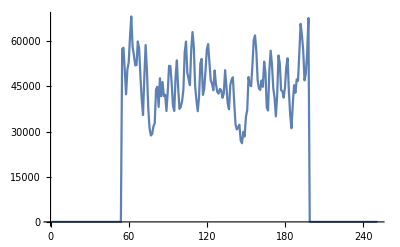

```mathematica
ListPlot[BC600["ci"],PlotRange->Full,Joined->True]
```

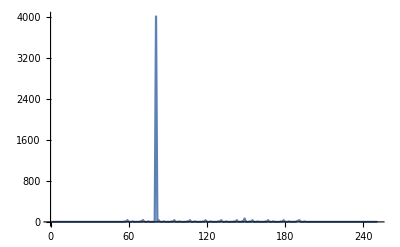

```mathematica
ListPlot[BC600["cs"],PlotRange->Full,Joined->True]
```

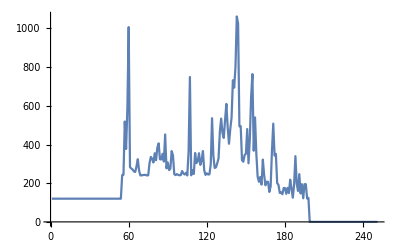

```mathematica
ListPlot[BC600["la"],PlotRange->Full,Joined->True]
```

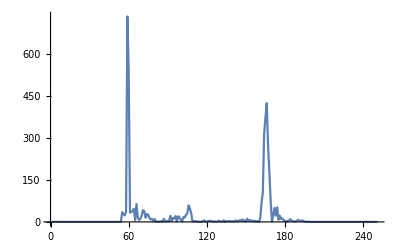

```mathematica
ListPlot[BC600["wk"],PlotRange->Full,Joined->True]
```

## 終端処理

```mathematica
end=AbsoluteTime[Date[]]
```

3.936784169843694×10^9

```mathematica
end-start
```

3722.808987